CHAPTER ChapterLabel

Calculus: Continuous and Discrete

Time may change me
But I can’t trace time
I said that time may change me
But I can’t trace time

David Bowie, “Changes”

ChapterLabel.Heading1  Introduction

This chapter primarily focuses on the types of problems students and teachers will cover in college-level mathematics courses and how Mathematica can be used as
a calculator (tool for getting an answer) and a teacher (tool for gaining insight into
a mathematical problem). However, this focus was largely pragmatic and does
not imply that Mathematica is limited to introductory calculus. Quite the contrary. Mathematica has been leading the charge among computer algebra systems since its inception, and with each new release the depth and breadth of its abilities in symbolic calculus improve. My goal in most of these recipes is to provide a starting point for the inexperienced user. Experts will probably find little that is new or highly original. This was a conscious choice based on space limitations. I am quite certain one could write a small cookbook by turning each recipe here into an entire chapter! Such is the depth of Mathematica’s abilities.

Most of the recipes in this chapter address what is commonly known as infinitesimal or continuous calculus. These problems deal with limits (Recipe 11.1), series (Recipe 11.3), derivatives (Recipe 11.4), integrals (Recipe 11.5), and differential
equations (Recipe 11.6). A common application of calculus is finding minimums and maximums. Mathematica packages these techniques into Minimize, Maximize, and related functions (Recipe 11.7). When you use your calculus skills to solve real engineering and physics problems, you are bound to run smack into applications that involve vector calculus. Mathematica has a package of functions specifically
dedicated to vector calculus, and we touch on some of this functionality in
Recipe 11.8.

Although the calculus of continuous functions still plays a dominant role, discrete calculus is extremely important and has been garnering increasing attention lately due to research in such varied domains as string theory, probability theory, theory of algorithms, and combinatorics, to name a few. Mathematica 7 has enhanced its discrete calculus abilities. Recipes 11.9 through 11.11 help you start using these capabilities.

See Also

A guide to all functions related to infinitesimal calculus can be found in the Mathematica documentation at guide/Calculus.

A guide to all functions related to discrete calculus can be found in the Mathematica documentation at guide/DiscreteCalculus.

ChapterLabel.Heading1  Computing Limits

Problem

You want to determine the value of a function as a variable approaches a specific value, even if evaluating the function at that limit may give an indeterminate result.

Solution

The functions Sin[x]/x, Sin[x^2]/x, and Sin[x]/x^2 each evaluate to the indeterminate value 0/0 at x = 0; however, their limits as x approaches zero are quite definite and different.

```mathematica
Limit[Sin[x]/x,x-> 0]
```

1

```mathematica
Limit[Sin[x^2]/x,x-> 0]
```

0

```mathematica
Limit[Sin[x]/x^2,x-> 0]
```

∞

Discussion

Plotting functions around the limiting value is often a good way to provide visual insight into the limiting value.

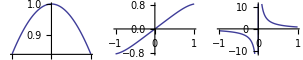

```mathematica
GraphicsRow[{Plot[Sin[x]/x,{x,-1,1}],Plot[Sin[x^2]/x,{x,-1,1}],Plot[Sin[x]/x^2,{x,-1,1}]}]
```

Here you can see that the last function has different limits depending on whether one approaches the limit from the left or the right. You can specify which limit you want using the option Direction.

```mathematica
(*From the left*)Limit[Sin[x]/x^2, x -> 0,Direction->1]
```

-∞

```mathematica
(*From the right*)Limit[Sin[x]/x^2, x -> 0, Direction -> -1]
```

∞

ChapterLabel.Heading1  Working with Piecewise Functions

Problem

You want to express a function in terms of two or more functions over different intervals.

Solution

Mathematica supports a function Piecewise for composing a complex function out of simpler functions using predicates to determine which of the simpler functions
apply.

```mathematica
f[x_] =Piecewise[{{Sqrt[1/x^2],x< -0.3}, {1/x, x >0.3 },{3.33,True}}]
```

Piecewise[{{√(1/x^2), x<-0.3}, {1/x, x>0.3}, {3.33, True}}]

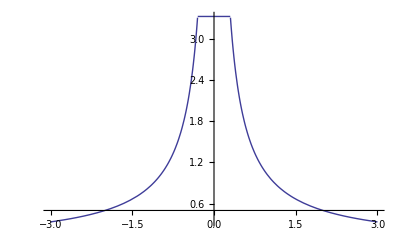

```mathematica
Plot[f[x],{x,-3,3}]
```

Discussion

Clip, Sign, and UnitStep are special cases of built-in piecewise functions. Clip constrains its input to a minimum and maximum value (default –1 and +1). Sign gives –1 or 1 depending on whether the input is negative or positive, and UnitStep is 0 for negative values and 1 for values greater than or equal to zero.

```mathematica
GraphicsRow[{Plot[Clip[2Sin[x]],{x,-Pi,Pi},PlotLabel->"Clip"],Plot[Sign[2Sin[x]],{x,-Pi,Pi},PlotLabel->"Sign"],Plot[UnitStep[2Sin[x]],{x,-Pi,Pi},PlotLabel->"UnitStep"]},ImageSize->{500,150}]
```

-Graphics-

You can differentiate and integrate piecewise functions, and you’ll get a piecewise function.

```mathematica
D[Clip[2Sin[x]],x]
```

Piecewise[{{0, Sin[x]<-1/2||Sin[x]>1/2}, {2 Cos[x], True}}]

```mathematica
Integrate[Clip[2Sin[x]],x]
```

Piecewise[{{-x, Sin[x]<-1/2}, {x, Sin[x]>1/2}, {-2 Cos[x], True}}]

PiecewiseExpand can take a nested piecewise function and return a single function. You can use this to show that Min, Max, and Abs are also special cases of piecewise functions.

```mathematica
PiecewiseExpand[Max[w,x,y,z]]
```

Piecewise[{{w, w-x≥0&&w-y≥0&&w-z≥0}, {x, w-x<0&&x-y≥0&&x-z≥0}, {y, w-y<0&&x-y<0&&y-z≥0}, {z, True}}]

```mathematica
PiecewiseExpand[Clip[Min[x,y]]]
```

Piecewise[{{-1, (x<-1&&x-y≤0)||(x-y>0&&y<-1)}, {1, (x>1&&x-y≤0)||(x-y>0&&y>1)}, {x, -1≤x≤1&&x-y≤0}, {y, True}}]

ChapterLabel.Heading1  Using Power Series Representations

Problem

You want to find the series expansion of a function.

Solution

The Mathematica function Series will generate the series expansion of a function about a point to a specified order. It produces a SeriesObject, which Mathematica will display as a traditional series expansion.

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
%//InputForm
```

SeriesData[x, 0, {1, 0, -1/6, 0, 1/120, 0, -1/5040, 0, 1/362880}, 1, 11, 1]

You use Normal to create a regular Mathematica expression. Here I also use
Evaluate because I am defining a function and want Normal to evaluate immediately even though the function is defined using SetDelayed (:=). Equivalently, you can use Set (=) to define the function without Evaluate.

```mathematica
f[x_] := Evaluate[Normal[Series[Sin[x],{x,0,10}]]]
```

You visualize the accuracy of the series approximation by plotting over successively larger intervals. As expected, this series approximation begins to diverge as you move away from the origin.

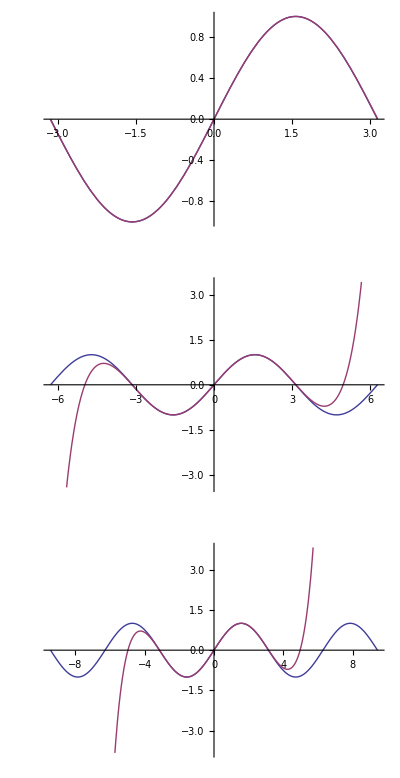

```mathematica
GraphicsColumn[Table[Plot[{Sin[x],f[x]},{x,-n Pi,n Pi}],{n,1,3}]]
```

Discussion

You can compute the inverse of a series using InverseSeries.

```mathematica
fInv[x_] = Normal[InverseSeries[Series[Sin[x],{x,0,10}]]]
```

x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152

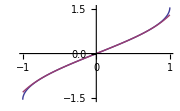

```mathematica
Plot[{ArcSin[x] ,fInv[x]},{x,-1,1},ImageSize->Small]
```

ChapterLabel.Heading1  Differentiating Functions

Problem

You want to compute derivatives or partial derivatives of functions in symbolic form. You may do this as a means of creating new functions or as a means of teaching the concepts that underlie differentiation.

Solution

Mathematica allows you to enter derivatives in input form as D[f[x], x] or in standard form as ∂_x f[x].

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[Sin[x], x]
```

Cos[x]

Higher-order derivatives are specified as D[f[x],{x,n}] where n is 2 for the second derivative, 3 for the third, and so on. In standard form, the second derivative can be entered as ∂_{x,2} f[x].

```mathematica
D[Sin[x],{x,2}]
```

-Sin[x]

Partial derivatives are easily accommodated as well using several equivalent notations.

```mathematica
D[Sin[x] Sin[y],{x,1}]
```

Cos[x] Sin[y]

```mathematica
D[Sin[x] Sin[y],x,x,y]
```

-Cos[y] Sin[x]

```mathematica
D[Sin[x] Sin[y],{x,2},{y,1}]
```

-Cos[y] Sin[x]

Discussion

Mathematica also recognizes prime notation, but this notation is more commonly used in Mathematica when entering a differential equation. See the sidebar “Mathematica’s Representation of Differentiation” on page 433 for some important subtleties.

```mathematica
{Sin'[x], Sin''[x]}
```

{Cos[x],-Sin[x]}

You can use D along with Solve to differentiate implicit functions. Simply use D as usual and use Solve to find the solution in terms of y'[x].

```mathematica
implicitFunction = x^4 + 2y[x]^2 == 8;
Solve[D[implicitFunction,x],y'[x]]
```

{{y'[x]→-x^3/y[x]}}

There are cases where you may want to use the D to synthesize a function on the fly. In this case, use Set (=) to perform the differentiation operation immediately or use Evaluate with SetDelayed (:=).

```mathematica
f1[x_] =D[Sin[Pi x Cos[x ^ 2]], x];
```

```mathematica
f2[x_] := Evaluate[D[Sin[Pi x Cos[x ^ 2]], x]]
```

```mathematica
{f1[2.], f2[2.]}
```

{-9.65614,-9.65614}

If you forget to do so, you will get an error when you call the function with a literal value.

```mathematica
f3[x_] :=D[Sin[Pi x Cos[x ^ 2]], x]
```

```mathematica
f3[2.]
```

General::ivar: 2. is not a valid variable.

∂_2. 0.82226

Mathematica’s Representation of Differentiation

More importantly, the prime notation is not synonymous with D[] but rather with a differential operator of the form Derivative[n]. The operator form clarifies ambiguities that would result from using it with functions of more than one variable. Think of Derivative[n1, n2, ...] as an operator that acts on a function to produce the specific derivative. The number of n’s should not exceed the number of variables of the function since each n is associated with the nth derivative of the corresponding variable. Some examples should help clarify.

First derivative with respect to x:

Derivative[1][f][x, y]

1-x^2/2+x^4/24-x^6/720+x^8/40320

f'[x,y]

1-x^2/2+x^4/24-x^6/720+x^8/40320

First derivative with respect to x, then y:

Derivative[1,1][f][x, y]

f^(1,1)[x,y]

f^(1,1)[x,y]

f^(1,1)[x,y]

First derivative with respect to x, then second derivative with respect to y:

Derivative[1,2][f][x, y]

f^(1,2)[x,y]

f^(1,2)[x,y]

f^(1,2)[x,y]

For the most part, you should work with D[] directly, but keep the operator notation in the back of your mind because it is how Mathematica represents derivatives internally.

D[f[x, y], x, y] // FullForm

Derivative[1,1][f][x,y]

Derivative[1,1][f][x,y]

f^(1,1)[x,y]

Many students will use Mathematica to check the answers to their calculus homework, but Mathematica is also useful for generating demonstrations of the fundamental concepts underlying differentiation. For example, the derivative of a function at a point is the slope of the tangent to the function at that point. Further, given two points, the slope of the secant drawn between these points approaches the derivative as the points approach each other along the curve. The following function uses
Mathematica’s dynamic features to generate presentations of this fact using any function and starting points as input.

```mathematica
makeDerivativeDemo[f_,x1_,x2_,opts:OptionsPattern[]] :=
 DynamicModule[{fp,f2, p1,p2,g,slope,slopeText,buildPlot,minX,maxX},
p1 = {x1,f[x1]};
p2 ={x2,f[x2]};
g=buildPlot[f,fp,f2,p1,p2];
With [{plotRange= Inner[{Min[##-3],Max[## +3]}&,p1,p2,List]},
minX= plotRange[[1,1]];
maxX = plotRange[[1,2]];
Dynamic[
Graphics[{g[[1]],Line[{p1,p2}],Locator[Dynamic[p1,{(p1={#[[1]],f[#[[1]]]})&,(g=buildPlot[f,fp,f2,p1,p2])&}],Appearance->Small],
Locator[Dynamic[p2,{(p2={#[[1]],f[#[[1]]]})&,(g=buildPlot[f,fp,f2,p1,p2])&}],Appearance->Small]},FilterRules[{opts},Options[g]],PlotRange-> plotRange,Options[g]]]
],
Initialization:>(
(*The actual derivative*)
fp[x_] := Evaluate[D[f[x],x]];
(*Function for tangent line at x0*)
f2[x0_,x_] := Module[{},f[x0] + fp[x0](x-x0)];
(*Text for slope of line from p1 to p2*)
slopeText[p1_,p2_] := Module[{s},s=Divide@@(1.0/(p2-p1));ToString[s]];
(*Plot function, tangent line, and text label*)
buildPlot[ff_,fp_,f2_,p1_,p2_] := Module[{},
Normal[Plot[{ff[x],f2[p1[[1]],x]}, {x, p1[[1]]-3,p2[[1]]+3},
Epilog->{Inset[Panel["Secant slope = " <> 
slopeText[p1,p2] <> 
"\nDerivative = " <>
ToString[N[fp[p1[[1]]]]]],{Left,Top},{Left,Top}]}
]]
]
)]
```

```mathematica
makeDerivativeDemo[Sin[Pi Cos[#]]&, 1.25,1.75]
```

ChapterLabel.Heading1  Integration

Problem

You want to solve problems that involve indefinite or definite integrals using symbolic integration.

Solution

Use Integrate or ∫ to compute single, double, or higher-order integrations. Indefinite integrals specify an expression and the variables of integration.

```mathematica
Integrate[1/x, x]
```

Log[x]

Definite integrals provide the minimum and maximum limits, which can be constants or expressions.

```mathematica
Integrate[1/x,{x,1,10.0}]
```

2.30259

```mathematica
Clear[a,b];
Integrate[x^2,{x,a,b}]
```

-a^3/3+b^3/3

The minimum and maximum limits can be -Infinity or Infinity.

```mathematica
Integrate[1/(x^3 + x^2),{x,1,Infinity}]
```

1-Log[2]

Discussion

Integrate will easily handle most integration problems you are likely to encounter in school, engineering, and science.

```mathematica
∫z^2/((z^2-1) √(z^2+1))ⅆz
```

1/4 (4 ArcSinh[z]+√2 (Log[-1+z]-Log[1+z]+Log[-1+z-√2 √(1+z^2)]-Log[1+z+√2 √(1+z^2)]))

Double and higher-order integrals are computed with a single Integrate function by adding multiple integration variables. However, if you use the traditional integration notation, you will use multiple integral symbols.

```mathematica
Integrate[Sin[2Pi z y/x] x y z,x,y,z]
```

1/(64 π^2)(x ((-2 π x^2 y z+4 π^3 y^3 z^3) Cos[(2 π y z)/x]+x (-3 x^2+2 π^2 y^2 z^2) Sin[(2 π y z)/x])+4 (x^4+2 π^4 y^4 z^4) SinIntegral[(2 π y z)/x])

```mathematica
∫∫∫x y zⅆxⅆyⅆz
```

1/8 x^2 y^2 z^2

Some integrations may return with conditionals and assumptions due to convergence issues. You can eliminate these by providing your own assumptions.

```mathematica
Integrate[Exp[-c x^2],{x,-∞,∞}]
```

If[Re[c]>0,(√π)/(√c),Integrate[ⅇ^(-c x^2),{x,-∞,∞},Assumptions→Re[c]≤0]]

```mathematica
Integrate[Exp[-c x^2],{x,-∞,∞},Assumptions-> c > 0]
```

(√π)/(√c)

You also do this using GenerateConditions → False.

```mathematica
Integrate[Exp[-c x^2],{x,-∞,∞},GenerateConditions -> False]
```

(√π)/(√c)

You can also get piecewise functions as a result of Integrate.

```mathematica
Integrate[Abs[x + Abs[x]^2],x, Assumptions-> x∈ Reals]
```

Piecewise[{{x^2/2+x^3/3, x≤-1}, {1/3-x^2/2-x^3/3, -1<x≤0}, {1/3+x^2/2+x^3/3, True}}]

When Integrate is unable to solve the integration, it will return the unevaluated integral in symbolic form.

```mathematica
Integrate[Exp[1/(Log[x]+1)],{x,2,3}]
```

∫_2^3 ⅇ^(1/(1+Log[x]))ⅆx

Applications of integration are numerous, and it would be impossible to provide even a small representative set of examples here. Rather, I will provide examples that emphasize how Integrate can be combined with other Mathematica functions in non-obvious ways.

A simple application is a function to compute the area between two arbitrary curves given two points. When you create functions that embed Integrate, you often want to allow options to pass through to increase generality.

```mathematica
areaBetweenTwoCurves[expr1_, expr2_, var_,a_,b_,opts:OptionsPattern[]] := Integrate[expr1 - expr2, {var,a,b}, Sequence @@ FilterRules[{opts},Options[Integrate]]]
```

```mathematica
areaBetweenTwoCurves[x,x^2,x,0,1]
```

1/6

This would generate a huge messy conditional if not for the ability to pass assumptions about the arbitrary bounds a and b.

```mathematica
areaBetweenTwoCurves[Log[x],Sin[x],x,a,b,Assumptions->a>0 && b>0]
```

a-b-Cos[a]+Cos[b]-a Log[a]+b Log[b]

Create a table of volumes of hyperspheres. Here Boole maps True to 1 and False
to 0. Note that the list of integration limits must be converted to a sequence using
Apply (@@). By the way, this is a very expensive way to calculate volume of a hypersphere, but it does illustrates how to parameterize the order of integration. Search for hyperspheres on Wikipedia or Wolfram’s MathWorld to find a more practical formula.

```mathematica
Table[Integrate[Boole[Sum[x[i]^2,{i,1,n}]≤1],Sequence @@ Table[{x[j],-Infinity,Infinity},{j,1,n}],GenerateConditions->True],{n,1,5}]
```

{2,π,(4 π)/3,π^2/2,(8 π^2)/15}

You can combine Integrate with differentiation to create a general function to compute the length of a curve between two points.

```mathematica
Clear[lengthOfCurve]
```

```mathematica
lengthOfCurve[expr_, var_,a_,b_,opts:OptionsPattern[]] := Integrate[Sqrt[1 + D[expr,var]^2],{var,a,b}, Sequence @@ FilterRules[{opts},Options[Integrate]]]
```

Or, you can compute the length of the hypotenuse of a right triangle.

```mathematica
lengthOfCurve[x,x,0,1]
```

√2

Verify the formula for the circumference of a circle given its radius by taking twice the arc length of a semicircle.

```mathematica
2 lengthOfCurve[Sqrt[r^2-x^2],x,-r,r,Assumptions-> r>0]
```

2 π r

Here is a purely symbolic solution with assumptions to simplify results.

```mathematica
lengthOfCurve[Exp[x],x,a,b,Assumptions->(a>0 && b>0)]
```

-√(1+ⅇ^(2 a))+√(1+ⅇ^(2 b))+1/2 Log[((1+√(1+ⅇ^(2 a))) (-1+√(1+ⅇ^(2 b))))/((-1+√(1+ⅇ^(2 a))) (1+√(1+ⅇ^(2 b))))]

ChapterLabel.Heading1  Solving Differential Equations

Problem

You have a model of a system described by a differential equation and you want to solve that equation symbolically. Two related problems are getting the equation in a form Mathematica expects and getting the solution in the form you expect.

Solution

An undergraduate student of engineering or physics will commonly need to solve differential equations that model simple systems. A common problem is an undamped oscillator composed of a mass hanging from a spring. The problem may appear in a textbook as

```mathematica
m y'' + k y = 0
```

This says that the force (mass × acceleration) is balanced by the force of the spring, as given by Hooke’s law, where k is the spring constant. The key to solving this equation in Mathematica using DSolve is to make the equation more explicit. Specifically, the equation omits the time variable. You must also replace the = symbol with == and tell Mathematica what equation we are solving for and what are the variables.

```mathematica
DSolve[m  y''[t] + k y[t] == 0, y[t],t]
```

{{y[t]→C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]}}

The solution is given as a replacement rule, and since the equation is a second order, two constants, C[1] and C[2], are introduced. You can provide initial conditions to eliminate the constants. In this case, you can also render the solution in its customary form by replacing Sqrt[k]/Sqrt[m] by the angular frequency ω.

```mathematica
DSolve[{m  y''[t] + k y[t] == 0,y[0] == 1,y'[0] ==1}, y[t],t] /. {Sqrt[k]/Sqrt[m] -> ω}
```

{{y[t]→(√k Cos[t ω]+√m Sin[t ω])/(√k)}}

Discussion

The solutions provided by DSolve are not automatically simplified, and you often will want to use Simplify or FullSimplify to postprocess them into a more mathematically friendly form. This is especially relevant when comparing the answer DSolve finds with answers provided in a typical textbook. Consider this problem adapted from Advanced Engineering Mathematics by Erwin Kreyszig (John Wiley). Here you want to find the solution to a differential equation describing the speed of a fluid flowing out of an opening in a container.

```mathematica
k= 0.00266 ;
eq = {h'[t] == -k Sqrt[h[t]],h[0] == 150};
sol =DSolve[eq,h[t],t]
```

{{h[t]→150.-0.0325782 t+1.7689×10^-6 t^2},{h[t]→150.+0.0325782 t+1.7689×10^-6 t^2}}

Given the physics of the problem, it should be clear we want the first solution (the second solution has the height increasing with time).

```mathematica
FullSimplify[sol[[1]]]
```

{h[t]→1.7689×10^-6 (-9208.61+t) (-9208.61+t)}

Although this has simplified the result somewhat, it is a much more complicated solution than the one provided by Kreyszig, which is

( √150-0.00133 t)^2

(5 √6-0.00133 t)^2

Did DSolve give the wrong result? A common mistake when using Mathematica is to prematurely substitute specific constants as I did above. It is often advisable to solve equations entirely in symbolic form and substitute constants later.

```mathematica
eq = {h'[t] == -k1 Sqrt[h[t]],h[0] == h0};
sol =FullSimplify[DSolve[eq,h[t],t][[1]]]
```

{h[t]→1/4 (-2 √h0+k1 t)^2}

Although this did not get us all the way to the form of the book’s solution, you are more likely to see the final transformation that will demonstrate that DSolve was correct. It hinges on noticing that 1/4 is the same as (–1/2)*(–1/2).

```mathematica
1/4 (-2 √h0+k1 t)^2 ==
 1/4 (-2 √h0+k1 t)(-2 √h0+k1 t)==
 -1/2 (-2 √h0+k1 t)-1/2(-2 √h0+k1 t) ==
( √h0-k1/2 t)( √h0-k1/2 t)==
( √h0-k1/2 t)^2
```

Substituting h0 and k1 with the constants shows that Mathematica did get the correct solution. Alternatively, you can ask Mathematica to prove its solution is equal to the book’s solution by using Resolve and ForAll. The only problem here is that Mathematica does not show its work!

```mathematica
Resolve[ForAll[{h0,k1,t},1/4 (-2 √h0+k1 t)^2 == ( √h0-k1/2 t)^2] ]
```

True

ChapterLabel.Heading1  Solving Minima and Maxima Problems

Problem

You want to find the minimum or maximum values of a function. You may need to find these extremes subject to constraints or for numbers in a specific domain (e.g., integers).

Solution

Although there are standard techniques used in calculus for finding extrema, Mathematica provides the specific functions Minimize and Maximize, which provide a great deal of power.

```mathematica
Maximize[1-(-2+x)^2-(-1+x)^4,x]//N
```

{0.710727,{x→1.58975}}

```mathematica
Minimize[2 x^4 - 3 x^2 + x,x]//N
```

{-2.0293,{x→-0.939693}}

Discussion

For many applications of minimization or maximization, you are interested in the extreme value within a specific interval.

```mathematica
Maximize[{((x-3)^3 -2x^2 - x), -1 < x < 4},x] //N
```

{-9.3726,{x→1.48085}}

I restrict this discussion to Maximize for simplicity, but everything here applies to Minimize as well. If you are interested in displaying the result of Maximize, you will want to force the result to numerical form, as we did in the solution. Maximize will keep the result in exact form if it is given input in exact form. For polynomials, this typically means the result will be expressed in terms of radicals or Root objects. A Root[f,k] object represents the kth solution to a polynomial equation f[x] == 0.

```mathematica
Maximize[{((x-3)^3 -2x^2 - x), -1 < x < 4},x]
```

{-27+26/3 (11-√43)-11/9 (11-√43)^2+1/27 (11-√43)^3,{x→1/3 (11-√43)}}

```mathematica
Maximize[1-(-2+x)^2-(-1+x)^4,x]
```

{-4+8 Root[-4+7 #1-6 #1^2+2 #1^3&,1]-7 Root[-4+7 #1-6 #1^2+2 #1^3&,1]^2+4 Root[-4+7 #1-6 #1^2+2 #1^3&,1]^3-Root[-4+7 #1-6 #1^2+2 #1^3&,1]^4,{x→Root[-4+7 #1-6 #1^2+2 #1^3&,1]}}

Sometimes you want to find solutions for integer values only. You can constrain Maximize to the integers in one of two ways. You might recognize this problem as an instance of a knapsack problem where you are optimizing the value of the knapsack (item1 has value 8, item2 11, and so on) subject to size constraint of 14 where item1 has size 5 and so on.

```mathematica
Maximize[{8x1 + 11 x2 + 6x3 + 4x4,5x1 +7x2+4x3+3x4 ≤ 14 && x1<2 && x2<2 && x3< 2 && x4 <2 && Element[x1|x2|x3|x4,Integers]},{x1,x2,x3,x4}]
```

{21,{x1→0,x2→1,x3→1,x4→1}}

A more convenient notation when all variables are integer is to specify the domain as the third argument to Maximize.

```mathematica
Maximize[{8x1 + 11 x2 + 6x3 + 4x4,5x1 +7x2+4x3+3x4 ≤ 14 && x1<2 && x2<2 && x3< 2 && x4 <2},{x1,x2,x3,x4},Integers]
```

{21,{x1→0,x2→1,x3→1,x4→1}}

Maximize seeks a global maximum, whereas an alternative function, FindMaximum, seeks a local maximum (there is also FindMinimum for local minimums). FindMaximum allows you to specify a starting point for the search, but otherwise has a very similar form to Maximize. The following program demonstrates the difference between Maximize and FindMaximum. The advantage of FindMaximum is that it does not require the objective function to be differentiable.

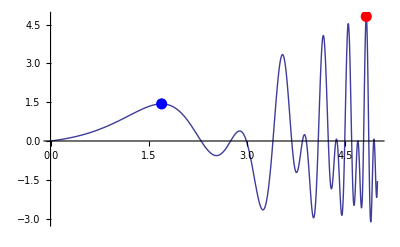

```mathematica
Clear["Global`*"];
f[x_] := x Cos[0.1 Exp[x]]Sin[0.1 Pi Exp[x]] ;
globalMax = Maximize[{f[x],0<x<5}, x];
localMax = FindMaximum[f[x], {x,0}];
Plot[f[x],{x,0,5},Epilog->{PointSize[0.02],
Red,Point[{x,f[x]}]/. Last[globalMax] ,
Blue, Point[{x,f[x]}]/. Last[localMax]}]
```

ChapterLabel.Heading1  Solving Vector Calculus Problems

Problem

You want to find solutions to problems within vector fields. Such problems arise in mechanics, electromagnetic theory, and fluid dynamics.

Solution

Simple vector calculus problems can be solved in terms of the calculus primitives discussed in this chapter’s recipes along with vector functions like Dot and Cross. For example, line integrals are commonly used to calculate work performed when moving a particle along a path in a vector field. Here F is the vector equation of the field, f is the equation of the path through the field, var is the parameter of f, and a and b are the start and end points of the path.

```mathematica
lineIntegral[F_, f_, var_, a_, b_] := Integrate[Dot[F[f[var]], D[f[var], var]], {var, a, b}]
F[{x_,y_,z_}] := {x+y,y^2,x-z}
f[t_] := {-t+1,t+2, -6 t +1}
lineIntegral[F,f,t,0,1]
```

-35/3

Another common operation in vector calculus is the surface integral over scalar functions and vector fields. Surface integrals are the 2D analog of line integrals. One way to think of the scalar surface integral is to imagine a surface f made of a material whose density varies as described by a second function g. The surface integral of f over g is then the mass per unit thickness.

```mathematica
surfaceIntegralScalar[g_, f_, {v1_,v1a_,v1b_}, {v2_,v2a_,v2b_}] := 
Integrate[g[f[v1,v2]]Norm[Cross[D[f[v1,v2],v1],D[f[v1,v2],v2]]],{v1,v1a,v1b},{v2,v2a,v2b}]
```

For example, consider the surface f1, which is a half sphere over the interval {ϕ, 0, Pi/2} and {θ, 0, 2 Pi}, and compute the surface integral given a density function given by (x^2 + y^2) z.

```mathematica
f1[ϕ_,θ_] := {Sin[ϕ]Cos[θ],Sin[ϕ]Sin[θ],Cos[ϕ]}
g1[{x_,y_,z_}] := (x^2 + y^2)z

surfaceIntegralScalar[g1,f1,{ϕ,0,Pi/2},{θ,0,2Pi}]
```

π/2

If we use a constant function (uniform density), we get the surface area of the half sphere as expected (surface area of an entire sphere is 4 πr^2).

```mathematica
g2[{x_,y_,z_}] :=1
surfaceIntegralScalar[g2,f1,{ϕ,0,Pi/2},{θ,0,2Pi}]
```

2 π

For a vector field, there is a similar equation using Dot in place of scalar multiplication by the norm. The traditional way to visualize the vector surface interval is to consider a fluid flowing through a surface where there is a vector function F describing the velocity of the fluid at various points on the surface. The surface integral is then the flux, or the quantity of fluid flowing through the surface in unit time.

```mathematica
surfaceIntegralVector[F_, f_, {v1_,v1a_,v1b_}, {v2_,v2a_,v2b_}] := Integrate[Dot[F[f[v1,v2]],Cross[D[f[v1,v2],v1],D[f[v1,v2],v2]]],{v1,v1a,v1b},{v2,v2a,v2b}]
```

Here is the solution to the flux described by {3 y, -z, x^2} through a surface described parametrically as {s t, s + t, (s^2 - t^2)/2}.

```mathematica
f[s_,t_] := {s t,s+t,(s^2-t^2)/2}
F[{x_,y_,z_}] := {3y,-z,x^2}
surfaceIntegralVector[F,f,{s,0,1},{t,0,3}]
```

-15

A standard result from electrostatics is that the net flux out of a unit sphere, for a field that is everywhere normal, is zero. We can verify this as follows:

```mathematica
F2[{x_,y_,z_}] := {1,1,1}/(x^2 + y^2 + z^2)
```

```mathematica
f2[θ_,ϕ_] := {Sin[ϕ]Cos[θ],Sin[ϕ]Sin[θ],Cos[ϕ]}
```

```mathematica
surfaceIntegralVector[F2,f2,{θ,0,2Pi},{ϕ,0,Pi}]
```

0

Discussion

The solution shows how the calculus primitives and other Mathematica functions can be used to build up higher-order vector calculus solutions. However, if you are interested in solving problems in vector calculus, the package VectorAnalysis` is definitely worth a look. Be forewarned that you might be in for a bit of a learning curve with this particular package, but it offers a lot of functionality. An important feature of the package is that it simplifies working in different coordinate systems.
Before you can make effective use of VectorAnalysis`, you need to understand how coordinate systems are used and which coordinate system is appropriate to your problem.

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
CoordinateSystem
```

Cartesian

```mathematica
SetCoordinates[Spherical]
```

Spherical[Rr,Ttheta,Pphi]

```mathematica
CoordinateSystem
```

Spherical

When you use VectorAnalysis`, you will typically want to use functions in that package in place of some standard Mathematica functions such as Dot and Cross. This is because the alternatives DotProduct and CrossProduct respect the current coordinate system. For example, if the current coordinate system is Spherical, you expect the following DotProduct to be zero because the vectors are orthogonal in spherical coordinates.

```mathematica
DotProduct[{1,Pi/2,0},{1,Pi/2,Pi/2}]
```

0

In contrast, Dot and Cross always assume Cartesian coordinates.

```mathematica
Dot[{1,Pi/2,0},{1,Pi/2,Pi/2}]
```

1+π^2/4

Some of the most important vector calculus operations are Div (divergence), Grad (gradient), Curl, and the Laplacian. Although it would make a nice exercise to implement these from the calculus primitives, as I did for line and surface integrals, there is no need if you use the VectorAnalysis` package. These operations use the default coordinate system, or you can specify a specific coordinate system as a separate argument.

The divergence represents the instantaneous outflow of a vector field at each point.

```mathematica
Together[Div[{1,1,1}/(x^2 + y^2 + z^2),Cartesian[x,y,z]]]
```

-(2 (x+y+z))/((x^2+y^2+z^2)^2)

The curl of a vector field represents the amount of rotation.

```mathematica
Together[Curl[{1, 1, 1}/(x^2 + y^2 + z^2), Cartesian[x, y, z]]]
```

{-(2 (y-z))/((x^2+y^2+z^2)^2),(2 (x-z))/((x^2+y^2+z^2)^2),-(2 (x-y))/((x^2+y^2+z^2)^2)}

By definition, the divergence of the curl must be zero since the curl has no net outflow.

```mathematica
SetCoordinates[Cartesian[x, y, z]];
Div[Curl[{1, 1, 1}/(x^2 + y^2 + z^2)]]
```

0

The gradient of a function f is a vector-valued function that indicates the direction in which f is increasing most rapidly. If you were climbing a hill, you would move in the direction of the gradient at each point to reach the top (strictly speaking the gradient would only be guaranteed to be directing you to a local peak). You can visualize the meaning of the gradient by using VectorPlot. I restrict the result to 2D for easier visualization.

```mathematica
GraphicsRow[{Plot3D[x^2 y^3,{x,-1,1},{y,-1,1},PlotRange->Full],
VectorPlot[Evaluate[Drop[Grad[ x^2 y^3 1,Cartesian[x,y,z]],-1]],{x,-1,1},{y,-1,1}]},ImageSize->500]
```

-Graphics-

See Also

The Mathematica tutorial to the VectorAnalysis package is essential reading for using those functions.

Div, Grad, Curl, and All That by H. M. Schey (W.W. Norton) and Vector Calculus by Paul C. Matthews (Springer) are two of my favorite informal introductions to vector calculus.

ChapterLabel.Heading1  Solving Problems Involving Sums 
and Products

Problem

You want to solve problems in discrete calculus that are expressed in terms of sums or products.

Solution

Mathematica can handle infinite sums and products with ease, provided, of course, they converge.

```mathematica
∑_(n=1)^∞ 1/n^2
```

π^2/6

```mathematica
∏_(i=2)^∞ (1 - 1/i^3)
```

Cosh[(√3 π)/2]/(3 π)

Discussion

If sums or products don’t converge, Mathematica will let you know by emitting an
error. You can test for convergence without evaluating the sum using SumConvergence.

```mathematica
∑_(n=1)^∞ 1/n
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/n

```mathematica
Table[{1/n^k,SumConvergence[1/n^k,n]},{k,1,4}]//TableForm
```

1/n | False
1/n^2 | True
1/n^3 | True
1/n^4 | True

As with Integrate, Sum can specify multiple summation variables. In traditional form these sums are rendered as a multiple summation, but keep in mind that these are entered as Sum[expr,{n,nmin,nmax},{m,mmin,mmaz}] rather than Sum[Sum[expr, {n,nmin,nmax}],{m,mmin,mmaz}].

This double summation has a surprisingly simply solution.

```mathematica
∑_(m=1)^∞ ∑_(n=1)^∞ (m^2 n)/(2^m (m 2^n+2^m n))
```

2

This is a very famous sum attributed to Srinivasa Ramanujan, one of India’s greatest mathematical geniuses. You might think that Mathematica is just doing some simple pattern matching to recognize this result; however, substitute for any of the magic constants in this formula, and Mathematica will handle it just as well (but don’t expect the answer to be as pretty).

```mathematica
(2 √2)/9801∑_(k=0)^∞ ((4k)!(1103 + 26390 k))/((k!)^4 396^(4k))
```

1/π

```mathematica
∑_(k=0)^∞ ((3k)!(5 + 10 k))/((k!)^4 300^(4k))
```

1/135000000(675000000 HypergeometricPFQ[{1/3,2/3},{1,1},1/300000000]+HypergeometricPFQ[{4/3,5/3},{2,2},1/300000000])

Here is a very pretty formula for π that combines an infinite sum and an infinite product.

```mathematica
(∏_(n=1)^∞ (1 + 1/(4 n^2-1)))/(∑_(n=1)^∞ 1/(4 n^2-1))
```

π

As of version 7, Mathematica can handle indefinite sums and products. Mathematica will seek to eliminate the sum if possible. For example, the sum over k of a polynomial is another polynomial that can be expressed in terms of k, and products over polynomials will invariably reduce to some expression involving Gamma.

```mathematica
∑_k (3 k^3-k^2+3 k+5)
```

1/12 k (40+33 k-22 k^2+9 k^3)

```mathematica
∏_k (k^2-3 k+5)
```

(3 Cosh[(√11 π)/2] Gamma[-3/2-(ⅈ √11)/2+k] Gamma[-3/2+(ⅈ √11)/2+k])/π

The Z-transform is an important infinite sum used in signal processing. It is defined as Sum[f[n] z^-n,{n,0,Infinity}], but is directly supported using ZTransform.

```mathematica
ZTransform[n^2,n,z]
```

(z (1+z))/(-1+z)^3

Here is an unconventional application for Sum, but one that is sometimes used in discrete math to introduce the idea of a generating function. You can use Sum to construct a generating function for solutions to problems like x1+x2+x3 == 12 subject to x1 >= 4, x2 >= 2, and 5 >= x3 >= 2. Each Sum is constructed from the smallest number the associated variable can take to the largest, by considering the smallest the other variables can take. For example, x1 must be at least 4 but can’t be greater than 12–2–2 = 8, since x2 and x3 must each be at least 2. Here we use Expand to generate the polynomial and Cases to find the exponents that sum to 12, thus giving all solutions.

```mathematica
Cases[ Expand[∑_(n=4)^8 x1^n∑_(n=2)^6 x2^n ∑_(n=2)^5 x3^n ],
x1^n1_ x2^n2_ x3^n3_ /; n1+n2+n3==12:>  {n1,n2,n3}]
```

{{8,2,2},{7,3,2},{6,4,2},{5,5,2},{4,6,2},{7,2,3},{6,3,3},{5,4,3},{4,5,3},{6,2,4},{5,3,4},{4,4,4},{5,2,5},{4,3,5}}

If you only care about the number of solutions, it would fall out of the coefficient of x^12 in the expansion of this polynomial.

```mathematica
Cases[ Expand[∑_(n=4)^8 x^n∑_(n=2)^6 x^n ∑_(n=2)^5 x^n ],a_ x^12 :> a]
```

{14}

See Also

See Recipe 11.11 for more information on generating functions in Mathematica.

Readers who are interested in gaining insight into the algorithms that underlie Mathematica’s amazing feats with infinite sums should read A=B by Marko Petkovsek, Herbert S. Wilf, and Doron Zeilberger (A K Peters), which is available online at http://bit.ly/1LJiwe.

ChapterLabel.Heading1  Solving Difference Equations

Problem

You want to solve problems that arise in discrete systems such as finance, actuarial science, dynamical systems, and numerical analysis. Many such problems can be modeled as recurrence relations, also known as difference equations.

Solution

RSolve is used to solve difference equations. A simple problem where RSolve applies is in mortgage calculations. Suppose you want to derive a function for the outstanding principal over the life of a loan. Let’s say the yearly interest rate is 5.75%, the monthly payment is $1,000.00, and the term is 30 years. This loan can be described as the following difference equation. Here the constraint y[360] == 0 arises from the condition that the last payment is zero (I am using y[0] as the origin).

```mathematica
i = 0.0575;
 payment = 1000.00; 
sol = RSolve[{y[n+1] == (1 + i/12) y[n] - payment,y[360]==0},y,n]
```

{{y→Function[{n},0.995231×2.71828^(-0.00478022 n) (209696.×1.00479^n-37516.4×1.00479^n 2.71828^(0.00478022 n))]}}

From this we can figure out the initial principal or the payoff at any given month:

```mathematica
y[0] /. sol[[1]]
```

171358.

After 60 months, or 5 years, very little has been paid off, which is quite depressing but a fact of life.

```mathematica
y[0] -y[60] /. sol[[1]]
```

12402.6

Discussion

Setting up a difference equation is often a matter of solving the problem by hand for small values of n and then detecting the relationship between successive values. Consider the Towers of Hanoi puzzle. A one-disk problem is solved in one move (T[1] = 1), a two-disk problem is solved in three moves (T[2] = 3), and three-disk problem is solved in seven moves (T[3] = 7). It follows then that T[n] = 2 T[n-1] + 1.

```mathematica
RSolve[{T[n] == 2 T[n-1] + 1, T[1] == 1},T,n]
```

{{T→Function[{n},-1+2^n]}}

A seemingly innocent difference equation can result in a solution involving complex numbers. This is a second-order equation, so two initial values are required to get an exact solution with no arbitrary constants.

```mathematica
sol = RSolve[{a[n] == 2(a[n-1] - a[n-2]),a[0]==1,a[1] == 2},a,n]
```

{{a→Function[{n},(1/2+ⅈ/2) ((1-ⅈ)^n-ⅈ (1+ⅈ)^n)]}}

Note that like DSolve, RSolve does not try to simplify the result. It is advisable to try to simplify it; in this case, you see that complex numbers disappear, and the result is in terms of trigonometric functions, which you may not have expected.

```mathematica
FullSimplify[a[n]/. sol[[1]]]
```

(1-ⅈ)^(-1+n)+(1+ⅈ)^(-1+n)

As with DSolve, if you do not provide initial conditions, you will get solutions involving arbitrary constants of the form C[N].

```mathematica
RSolve[{a[n] -3 a[n-1] == 5(3^n)},a,n]
```

{{a→Function[{n},5 3^n n+3^(-1+n) C[1]]}}

These solutions were found in terms of pure functions because we asked for the solution in terms of a, but you can change the form of the second argument to a[n] to get the solution in that form.

```mathematica
sol =RSolve[{a[n] -3 a[n-1] == 5(3^n)},a[n],n]
```

{{a[n]→5 3^n n+3^(-1+n) C[1]}}

You can evaluate this solution for specific n and C[1] using ReplaceAll (//.).

```mathematica
a[n] //. Flatten[{sol,n->3, C[1] -> 2}]
```

423

See Also

One of the best introductions to the subject of difference equations is An Introduction to Difference Equations by Saber Elaydi (Springer).

ChapterLabel.Heading1  Generating Functions 
and Sequence Recognition

Problem

You want Mathematica to generate a function associated with a particular sequence or to infer a function that will produce the sequence for successive integers.

Solution

Use FindGeneratingFunction to derive the generating function for a sequence.
Recall that the power series of a generating function encodes the sequence in its
coefficients.

```mathematica
g =FindGeneratingFunction[{1,4,9,16,25,36,49,64,81,100},x]
```

(-1-x)/(-1+x)^3

```mathematica
Series[g,{x,0,12}]
```

1+4 x+9 x^2+16 x^3+25 x^4+36 x^5+49 x^6+64 x^7+81 x^8+100 x^9+121 x^10+144 x^11+169 x^12+O[x]^13

Use FindSequenceFunction to find an expression that maps the integers to the specified sequence.

```mathematica
s =FindSequenceFunction[{1,4,9,16,25,36,49,64,81,100},n]
```

n^2

```mathematica
Table[s,{n,1,12}]
```

{1,4,9,16,25,36,49,64,81,100,121,144}

Discussion

FindSequenceFunction can deal with sequences that are not strictly increasing and with noninteger sequences.

```mathematica
FindSequenceFunction[{-1,3,-11,13,-29,31,-55,57,-89,91,-131,133,-181,183,-239},n]//FullSimplify
```

(-1)^n (-(-1)^n (-1+n)+n^2)

```mathematica
FindSequenceFunction[{0,2/9,3/8,12/25,5/9,30/49,21/32,56/81,18/25,90/121},x]
```

(-x+x^2)/(1+x)^2

You can synthesize a generating function from an expression using GeneratingFunction.

```mathematica
g =GeneratingFunction[1/((n+1)!),n,x]
```

(-1+ⅇ^x)/x

And recover the sequence to the Nth term using the following expression:

```mathematica
With[{N=12},1/Table[SeriesCoefficient[Simplify[Series[g,{x,0,N}]],n],{n,1,N}]]
```

{2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800}

See Also

For the nonexpert, a very approachable book on generating functions is Generatingfunctionology by Herbert S. Wilf (A K Peters). An online version can be found at http://bit.ly/3bkssK.